# Constructing the secular Hamiltonian

## Evaluating integrals of multi-pole terms

Here I consider the secular evolution of a test particle interior to a (possibly eccentric) perturber, p. The Hamiltonian governing secular interactions is given by the “double-averaged” potential:
	ℋ_sec= -1/(4 π^2)(∫_0)^(2π)ⅆl(∫_0)^(2π)ⅆ l_p(G m_p)/(|r-r_p|)
	= -(G m_p)/(4 π^2 a_p)(∫_0)^(2π)ⅆl(∫_0)^(2π)ⅆ l_p  (∑_(j=2))^∞ α^j (r/a)^j(a_p/r_p)^(j+1)P_j[cos(Φ)]
where the second line gives the multi-pole expansion of  the potential in Legendre polynomials. 

I will use a coordinate system in which the x-y plane is the orbital plane of the perturber and the x direction is towards the pericenter of the perturber. In this coordinate system
	cos[Φ] = 1/(1-e_p cos[u_p])(cos[u_p]-e_p,√(1-e_p^2)sin[u_p],0)·(X,Y,Z)
	 =(1-e_p cos[u_p])^-1[(cos[u_p]-e_p)X + √(1-e_p^2)sin[u_p]Y]
where u_p is the perturbers eccentric anomaly and (X,Y,Z) are the coordinates of the test particle’s position unit vector (explicit expressions to be given below.)

Integral of l_p

Integration over l_p can be done as follow:
	- First we will use ⅆ l_p=(1-e_p cos[u_p])ⅆ u_pto do the integral over eccentric anomaly

	- Note that r_p/a_p=1-e_p cos[u_p]

	- From the expression for cos[Φ] it is clear that the integrand is a series of terms of the form:
		(1-e cos[u_p])^-n cos^k_c[u_p]sin^k_s[u_p]

	- If k_s is odd then the integrand term is an odd function and its integral=0.  

	- If k_s is even, make the replacement sin[u_p]^2=1-cos[u_p]^2. Thus, all non-zero integrand terms can be expressed in the 	form:
		 (1-e cos[u_p])^-n cos^k[u_p]

Defining 
	 I_(n,k)(a,e)=1/(2π)(∫_0)^(2π)ⅆu  (a-e cos[u])^-n cos[u]^k
the recursion relations:
	 I_(1,0)(a,e)=1/(√(a^2-e^2))
I_(n,0)(a,e)=-1/(n-1)ⅆ/ⅆa I_(n-1,0)(a,e)
I_(n,k)(a,e)=1/(n-1)ⅆ/ⅆe I_(n-1,0)(a,e)
can be used to compute all integral terms by evaluating I_(n,k)(1,e_p).

```mathematica
int[1,0]:=1/(√(a^2-ep^2));
int[n_Integer,0]:=D[-1/(n-1)int[n-1,0],a]; 
int[n_Integer,k_Integer]:=1/(n-1)D[int[n-1,k-1],ep]/;k<n
```

Below 
	s=sin[u_p]
 c = cos[u_p]  
d = 1-e_p cos[u_p]

```mathematica
potentialTerm[j_]:=ExpandAll[d^-j LegendreP[j,(c-ep)/d X+√(1-ep^2)s/d Y]];
```

```mathematica
integrationRule={

Times[x__,Power[d,n_],Power[c,k_]]:> Times[x,int[-n,k]/.a->1],
Times[x__,Power[d,n_],c]:> Times[x,int[-n,1]/.a->1],
Times[x__,Power[d,n_]]:> Times[x,int[-n,0]/.a->1]
};
```

```mathematica
doIntegralOverlp[terms_]:=Simplify[ExpandAll[terms/.s^2->1-c^2/.s->0]/.integrationRule]
```

```mathematica
doIntegralOverlp[potentialTerm[2]]
```

(-2+3 X^2+3 Y^2)/(4 (1-ep^2)^(3/2))

Integral of l

Integration over the particle’s mean longitude is done as follows:
- First, the coordinates of the particle are given by R_z(h)R_x(i)R_z(g)·((cos[u]-e)/(1-e cos[u]),(√(1-e^2)sin[u])/(1-e cos[u]),0) where u is the particle’s eccentric anomaly.
- Replacing r/a=1-e cos[u] and ⅆl = (1-e cos[u])ⅆu, the integrand involves a series of monomials  (1-e cos[u])^(j+1)X^n Y^m.
- The integral can be re-written as a series of monomials in sin[u] and cos[u]. 
- Integration over u is then straightforward (Its straightforward to  to verify that no factors  of (1-e cos[u]) will be present in the denominator of the integrand terms, unlike the integral over l_p

```mathematica
particleCoodinatesRule=Thread[{X,Y,Z}->EulerMatrix[{h,ArcCos[θ],g},{3,1,3}].{(c-e)/(1-e*c),√(1-e^2)s/(1-e*c),0}];
sincosToComplex = {c->(1/2(z+1/z)),s->(1/(2*I)(z-1/z))};
```

```mathematica
integralOverU[expression_]:=Coefficient[ExpandAll[expression/.sincosToComplex],z,0]
```

```mathematica
multipoleTerm[j_]:=α^j Simplify[

integralOverU[(1-e*c)^(j+1)doIntegralOverlp[potentialTerm[j]]/.particleCoodinatesRule]

]
```

## The Hamiltonian to octupole order

```mathematica
quadrupole=multipoleTerm[2];
```

```mathematica
octupole=TrigReduce[multipoleTerm[3]];
```

Compare the expressions below with equations 8-11 in Lithwick+Naoz (2011):

```mathematica
ExpandAll[(8(1-ep^2)^(3/2))/(3 α^2)quadrupole]
Simplify[Coefficient[(8(1-ep^2)^(5/2))/(3 α^3 ep)*16/5 octupole,{Cos[g+h],Cos[g-h],Cos[3g-h],Cos[3g+h]}]]
```

-1/3-e^2/2+θ^2+(3 e^2 θ^2)/2+5/2 e^2 Cos[2 g]-5/2 e^2 θ^2 Cos[2 g]

{-1/4 e (4+3 e^2) (-1-11 θ+5 θ^2+15 θ^3),1/4 e (4+3 e^2) (1-11 θ-5 θ^2+15 θ^3),-35/4 e^3 (-1+θ)^2 (1+θ),35/4 e^3 (-1+θ) (1+θ)^2}

Replace orbital elements with dynamical variables, J and Jz

```mathematica
(* Add constant term '1/3' to match energy levels listed in LN11, doesn't affect dynamics *)
Fqu = ExpandAll[((8(1-ep^2)^(3/2))/(3 α^2)quadrupole+1/3)/.θ->Jz[t]/(√(1-e^2))/.e^2->1-J[t]^2/.g->g[t]/.h->h[t]];
Foc =TrigReduce[ Simplify[((8(1-ep^2)^(5/2))/(3 α^3 ep)octupole)/.θ->Jz[t]/(√(1-e^2))/.e->√(1-J[t]^2)/.g->g[t]/.h->h[t],Assumptions->J[t]>0]];
```

Symplectic matrix:

```mathematica
Clear[Jmatrix];
Jmatrix[n_Integer] := ArrayFlatten[{
    {Array[0 &, {n, n}], IdentityMatrix[n]},
    {-IdentityMatrix[n], Array[0 &, {n, n}]}
    }];
```

Integrate equations of motion

```mathematica
vars={g[t],h[t],J[t],Jz[t]};
```

With z := (q,p) the equations of motion are given by: ⅆz/ⅆt = J∇_z ℋ

```mathematica
equationsOfMotion = Thread[D[vars,t]==Jmatrix[2].Grad[Fqu,vars]];
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
```

Specify  initial conditions (setting J_z=0.2 to match Figure 1 of LN11):

```mathematica
initsrule={g0->Pi/2,h0->0,e0->0.5,θ0->0.2/(√(1-e0^2))};
```

Integrate equations of motion

```mathematica
tStop = 1;
soln=NDSolve[Evaluate[Join[equationsOfMotion,initalCondtions]//.initsrule],(vars/.x_[t]:>x),{t,0,tStop}];
```

Expression for use in contour plot

```mathematica
Hexprn=Fqu/.{g[t]->g,Jz[t]->0.2,J[t]->0.2/θ};
```

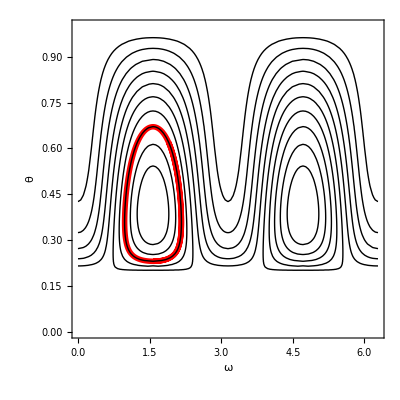

```mathematica
Show[
(* Plot result of integration *)
ParametricPlot[Evaluate[{g[t],Jz[t]/J[t]}/.soln],{t,0,1},AspectRatio->1,Frame->True,PlotStyle->Directive[Red,Thickness[0.01]]],

(* Contour plot showing level curves of the Hamiltonian *)
ContourPlot[Hexprn,{g,0,2Pi},{θ,0.2,1},Contours->10,ContourShading->None],

(* Plot options*)
PlotRange->{{0,2Pi},{0.0,1}},
Axes->False,
FrameLabel->{ω,θ},
FrameStyle->Directive[16,Black]
]
```

## surface of section with octupole term included

```mathematica
ϵ=0.01;
ℋ=Fqu+ϵ Foc;
equationsOfMotion = Thread[D[vars,t]==Jmatrix[2].Grad[ℋ,vars]];
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
```

```mathematica
replaceRule=(initalCondtions/.Equal->Rule/.x_[0]:>x[t]);
```

```mathematica
ruleΩPi={g0->0,h0->Pi,e0->e,θ0->θ};
ruleΩ0={g0->0,h0->0,e0->e,θ0->θ};
exprnΩPi=(Fqu)+ϵ Foc/.replaceRule/.ruleΩPi;
exprnΩ0=(Fqu)+ϵ Foc/.replaceRule/.ruleΩ0;
```

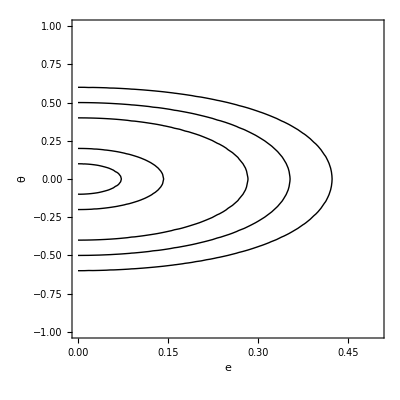

```mathematica
ContourPlot[exprnΩPi,{e,0,0.5},{θ,-1,1},Contours->{0.01,0.04,0.16,0.25,0.36},ContourShading->None,FrameLabel->{e,θ,"Constant Energy Contours"},FrameStyle->Directive[Black,18]]
```

Section for single trajectory

Integrate equations of motion and record points

```mathematica
Elevel = 0.16
```

0.16

```mathematica
initsrule=ruleΩPi/.First[FindInstance[exprnΩPi==Elevel&&e>0&&θ==0.3,{e,θ}]];
```

```mathematica
{soln,pts}=Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{g,Jz[t],J[t]},{t,0,160}
];
```

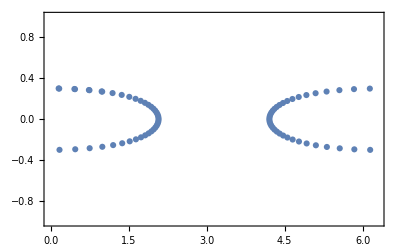

```mathematica
ListPlot[pts,PlotRange->{{0,2Pi},{-1,1}},Frame->True]
```

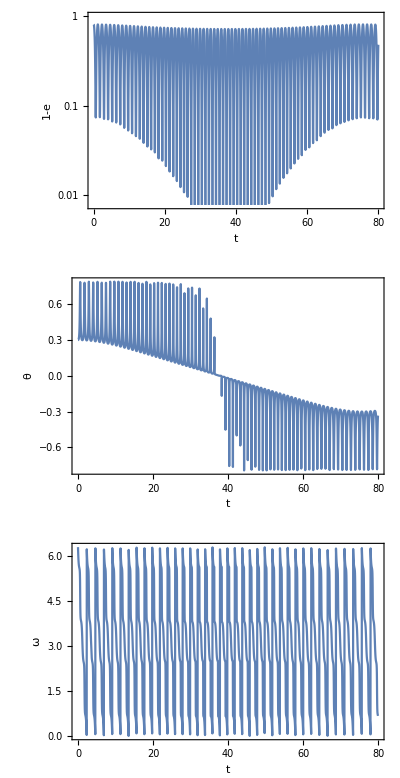

```mathematica
GraphicsColumn@{
LogPlot[1-√(1-J[t]^2)/.soln,{t,0,80},Frame->True,FrameLabel->{t,1-e}],
Plot[Jz[t]/J[t]/.soln,{t,0,80},Frame->True,FrameLabel->{t,θ}],
Plot[Mod[g[t]/.soln,2Pi],{t,0,80},Frame->True,FrameLabel->{t,ω}]
}
```

Show multiple trajectories

```mathematica
Elevel = 0.16;
```

```mathematica
allpts=Table[
initsrule=ruleΩPi/.First[FindInstance[exprnΩPi==Elevel&&e>0&&θ==θ0,{e,θ}]];
Last@Last@Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{},{t,0,160}
]
,
{θ0,Most@Rest@Subdivide[0,√Elevel,8]}];
```

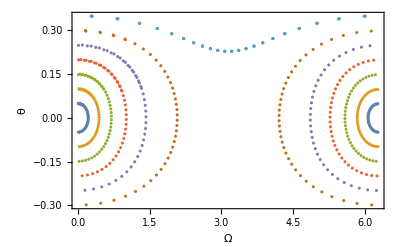

```mathematica
ListPlot[allpts,
Frame->True,FrameLabel->{Ω,θ},
FrameStyle->Directive[Black,18]]
```